```mathematica
(*Author: Oleg Kravchenko, Date: 05/12/15*)
```

```mathematica
ClearAll["Global`*"]
```

#### Parameters;

```mathematica
imgSize=300;
```

#### R - operators;

```mathematica
RCon[x_,y_]:=0.5(x+y-Sqrt[x^2+y^2])
RDiz[x_,y_]:=0.5(x+y+Sqrt[x^2+y^2])
```

#### Functions;

```mathematica
f03[x_,y_]:=x+0.5
f04[x_,y_]:=y+0.5
f05[x_,y_]:=0.5-x
f06[x_,y_]:=0.5-y
Subscript[ω, H][x_,y_]:=RCon[f03[x,y],f04[x,y]]
Subscript[ω, C][x_,y_]:=RCon[f05[x,y],f06[x,y]]
ω[x_,y_]:=(Subscript[ω, C][x,y])/(Subscript[ω, H][x,y]+Subscript[ω, C][x,y])
```

```mathematica
Row[{Plot3D[{f03[x,y],f04[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize],
Plot3D[{f05[x,y],f06[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize]}]
```

-Graphics3D--Graphics3D-

```mathematica
Row@{Plot3D[{Subscript[ω, H][x,y],Subscript[ω, C][x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize],
Plot3D[{ω[x,y],Subscript[ω, H][x,y],Subscript[ω, C][x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize]}
```

-Graphics3D--Graphics3D-

```mathematica
{dωx,dωy}={D[ω[x,y],x],D[ω[x,y],y]};
%//Simplify//Column//TraditionalForm
```

((0.25 (√(x^2-1. x+y^2-1. y+0.5)+x-0.5) (1. √(x^2-1. x+y^2-1. y+0.5)+1. √((x+0.5)^2+(y+0.5)^2)-2.))/(√(x^2-1. x+y^2-1. y+0.5))-0.5 (-1. √(x^2-1. x+y^2-1. y+0.5)-x-y+1.) (0.5 ((0.5-1. x)/(√(x^2-1. x+y^2-1. y+0.5))-1)+0.5 (1-(x+0.5)/(√((x+0.5)^2+(y+0.5)^2)))))/(-0.5 √(x^2-1. x+y^2-1. y+0.5)-0.5 √(x^2+1. x+y^2+1. y+0.5)+1.)^2
((0.25 (√(x^2-1. x+y^2-1. y+0.5)+y-0.5) (1. √(x^2-1. x+y^2-1. y+0.5)+1. √((x+0.5)^2+(y+0.5)^2)-2.))/(√(x^2-1. x+y^2-1. y+0.5))-0.5 (-1. √(x^2-1. x+y^2-1. y+0.5)-x-y+1.) (0.5 ((0.5-1. y)/(√(x^2-1. x+y^2-1. y+0.5))-1)+0.5 (1-(y+0.5)/(√((x+0.5)^2+(y+0.5)^2)))))/(-0.5 √(x^2-1. x+y^2-1. y+0.5)-0.5 √(x^2+1. x+y^2+1. y+0.5)+1.)^2

```mathematica
Laplacian[ω[x,y],{x,y}]/.x->-0.5/.y->-0.25
```

14.4

```mathematica
Row@{Plot3D[{dωx},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize,PlotRange->All],
Plot3D[{dωy},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize,PlotRange->All],
Plot3D[{dωx-dωy},{x,-0.5,0.5},{y,-0.5,0.5},PlotStyle->Opacity[0.95],Mesh->None,ImageSize->imgSize,PlotRange->All]}
```

-Graphics3D--Graphics3D--Graphics3D-

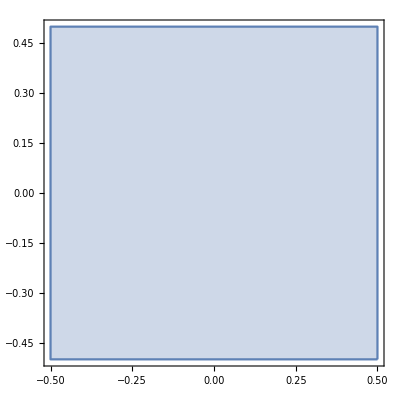

```mathematica
Ω=Rectangle[{-1/2,-1/2},{1/2,1/2}];
RegionPlot[Ω]
```

```mathematica
usol01=NDSolveValue[{Laplacian[u[x,y],{x,y}]==ω[x,y],
{DirichletCondition[u[x,y]==1,x== -0.50],
DirichletCondition[u[x,y]==1,y== -0.50],
DirichletCondition[u[x,y]==0,x== +0.50],
DirichletCondition[u[x,y]==0,y== +0.50]}
},u,{x,y}∈Ω]
```

InterpolatingFunction[{{-0.5, 0.5}, {-0.5, 0.5}}, <>]

```mathematica
Row@{Plot3D[ω[x,y],{x,y}∈Ω],Plot3D[usol01[x,y],{x,y}∈Ω]}
```

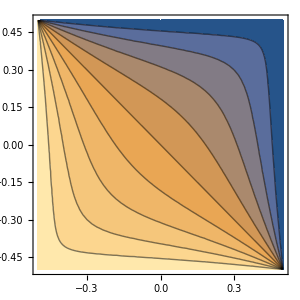
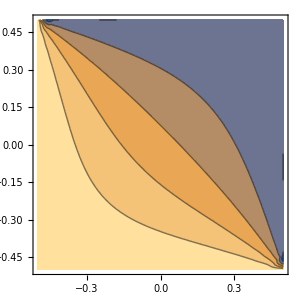

```mathematica
Row@{ContourPlot[ω[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ImageSize->imgSize],
ContourPlot[usol01[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ImageSize->imgSize]}
```

```mathematica
usol02=NDSolveValue[{Laplacian[u[x,y],{x,y}]==-Laplacian[ω[x,y],{x,y}],
DirichletCondition[u[x,y]==0,{x,y}∈Ω]
},u,{x,y}∈Ω]
```

InterpolatingFunction[{{-0.5, 0.5}, {-0.5, 0.5}}, <>]

```mathematica
ωDel2=Laplacian[ω[x,y],{x,y}];
```

```mathematica
Row@{Plot3D[usol02[x,y],{x,y}∈Ω,ImageSize->imgSize],Plot3D[ωDel2,{x,-0.5,0.5},{y,-0.49,0.49},ImageSize->imgSize,PlotRange->Full]}
```

-Graphics3D--Graphics3D-

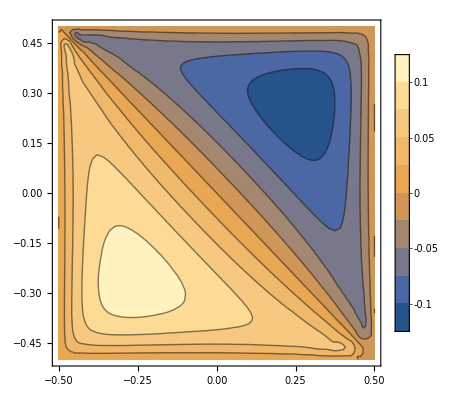

```mathematica
ContourPlot[usol02[x,y],{x,-0.5,0.5},{y,-0.49999,0.49999},PlotRange->Full,PlotLegends->Automatic]
```

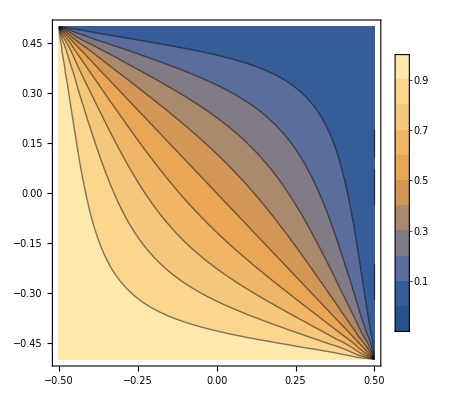

```mathematica
ContourPlot[usol02[x,y]+ω[x,y],{x,-0.5,0.5},{y,-0.49999,0.49999},PlotRange->Full,PlotLegends->Automatic]
```